# Лабораторная работа №6

## Дискретные математические модели

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
апрель 2022
ММФ, КМ и СА, доц. Лаврова О.А., доц. Щеглова Н.Л.

## Задание 1. Дискретные модели популяционной динамики

Рассмотрим дискретные динамические системы, которые используются в качестве математических моделей популяционной динамики:

Модель Бевертона-Холта

N_(n+1)=(k N_n)/(1+ N_n),      гдеk=const>0.

Безразмерная модель Рикера

N_(n+1)=N_n ⅇ^(k(1-N_n)), гдеk=const>0.

### Задание 1.1 (Неподвижные точки)

Найдите неподвижные точки N^* дискретных динамических систем (1) и (2) при условии, что численность популяции N≥0.

N_(n+1)=(k N_n)/(1+N_n), где k = const > 0;
Неподвижные точки:
N^*=(k N^*)/(1+N^*);
В дальнейшем опустим * в обозначениях.
N (1-k/(1+N)) = 0
N_1 = 0 или 1 = k/(1+N_2)
1+N_2 = k   ==>   N_2 = k-1, причем N_2 ≠ -1 (что, вообще говоря, не может быть такого случая);

N_(n+1)=N_n ⅇ^(k(1-N_n)), где k = const > 0;
Неподвижные точки:
N^*= N^* ⅇ^(k(1-N^*));
В дальнейшем опустим * в обозначениях.
N (1-ⅇ^(k(1-N))) = 0
N_1 = 0 или 1 = ⅇ^(k(1-N_2))
k(1-N_2) = 0 ;
N_2 = 1;

Исследуйте неподвижные точки на устойчивость.

N_(n+1)=(k N_n)/(1+N_n), где k = const > 0;
f(N)=(k N)/(1+N);
f '(N) = (k+kN-kN)/(1+N)^2 = k/(1+N)^2;

Рассмотрим устойчивость неподвижной точки N_1 = 0:
f ‘(0)  = k/(1+0)^2 = k
Следовательно, неподвижная точка N_1 = 0, учитывая, что k = const > 0, является асимптотически устойчивой  при 0 < k < 1 и неустойчивой при k > 1.

Рассмотрим устойчивость неподвижной точки N_2 = k - 1:
f ‘(k-1)  = k/(1+k-1)^2 = 1/k
Следовательно, неподвижная точка N_2 = k - 1, учитывая, что, в данном случае, k = const  ≥ 1 (так как N ≥ 0),  является асимптотически устойчивой .

N_(n+1)=N_n ⅇ^(k(1-N_n)), где k = const > 0;
f(N) = N ⅇ^(k(1-N));
f '(N) = ⅇ^(k(1-N))-k N ⅇ^(k (1-N)) = ⅇ^(k(1-N)) (1 - k N);

Рассмотрим устойчивость неподвижной точки N_1 = 0:
f ‘(0)  = ⅇ^(k(1-0)) (1 - k*0) = ⅇ^k
Следовательно, неподвижная точка N_1 = 0, учитывая, что k = const > 0, является  неустойчивой.

Рассмотрим устойчивость неподвижной точки N_2 = 1:
f ‘(1)  = ⅇ^(k(1-1)) (1 - 1*k) = 1 - k
Следовательно, неподвижная точка N_2 = 1, учитывая, что k = const  > 0,  является асимптотически устойчивой при 0 < k < 2 и неустойчивой при k > 2.

Найдите первые бифуркационные значения параметров -- значения параметров, при которых собственное значение одномерной дискретной динамической системы, вычисленное в неподвижной точке, равно по модулю 1.

Для N_(n+1)=(k N_n)/(1+N_n), где k = const > 0 , f(N) = (k N)/(1+N), первые бифуркационные значения параметров -- значения параметров, при которых собственное значение одномерной дискретной динамической системы, вычисленное в неподвижной точке, равна 1 и при этом данная точка устойчива.

Для N_(n+1)=N_n ⅇ^(k(1-N_n)), где k = const > 0 , f(N) = N ⅇ^(k(1-N)), первые бифуркационные значения параметров -- значения параметров, при которых собственное значение одномерной дискретной динамической системы, вычисленное в неподвижной точке, равна 2.

### Задание 1.2 (Графики решений)

Постройте графики решений дискретных динамических систем (1) и (2) для начальных состояний N_0, взятых в окрестности неподвижных точек N^*. При этом постройте решения при различных значениях параметра k, когда одна и та же неподвижная точка N^* является абсолютно устойчивой или неустойчивой.

Для построения решений дискретных динамических систем можно использовать функцию RecurrenceTable.

```mathematica
?RecurrenceTable
```

Пример построения последовательности чисел Фибоначчи как решения двумерной дискретной динамической системы

```mathematica
RecurrenceTable[{fib[n+1]==({{1, 1}, {1, 0}}).fib[n],fib[0]=={1,1}},fib,{n,0,20}][[;;,2]]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946}

```mathematica
Table[Fibonacci[n],{n,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

N_(n+1)=(k N_n)/(1+N_n), где k = const > 0;
f(N)=(k N)/(1+N);
f '(N) = (k+kN-kN)/(1+N)^2 = k/(1+N)^2;

Рассмотрим устойчивость неподвижной точки N_1 = 0:
f ‘(0)  = k/(1+0)^2 = k
Следовательно, неподвижная точка N_1 = 0, учитывая, что k = const > 0, является асимптотически устойчивой  при 0 < k < 1 и неустойчивой при k > 1.

Рассмотрим устойчивость неподвижной точки N_2 = k - 1:
f ‘(k-1)  = k/(1+k-1)^2 = 1/k
Следовательно, неподвижная точка N_2 = k - 1, учитывая, что, в данном случае, k = const  ≥ 1 (так как N ≥ 0),  является асимптотически устойчивой .

```mathematica
Manipulate[{{TextCell[
If[k<1,StringForm["k= ``< 1\n Неподвижная точка N = 0 является асимптотически устойчивой",k],
If[k>1,StringForm["k= ``> 1\n Неподвижная точка N = 0 является неустойчивой",k],
If[k==1,StringForm["k= ``== 1\n Бифуркационная неподвижная точка N = k - 1",k]]]],
"Output"]},
{ListLinePlot[RecurrenceTable[{NN[n+1]==(k NN[n])/(1+NN[n]),NN[0]==0+10^-4},NN,{n,1,100}],PlotRange->Full,ImageSize->Medium]}},
{{k,1},0.1,5,0.1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[{{TextCell[
If[1/k<1,StringForm["1/k= ``< 1\n Неподвижная точка N = k - 1 является асимптотически устойчивой",1/k],
If[1/k>1,StringForm["1/k= ``> 1\n Неподвижная точка N = k - 1 является неустойчивой",1/k],
If[1/k==1,StringForm["1/k= ``== 1\n Бифуркационная неподвижная точка N = k - 1",1/k]]]],
"Output"]},
{ListLinePlot[RecurrenceTable[{NN[n+1]==(k NN[n])/(1+NN[n]),NN[0]==k-1+10^-4},NN,{n,1,100}],PlotRange->Full,ImageSize->Medium]}},
{{k,1},0.1,5,0.1,Appearance->"Labeled"}]
```

N_(n+1)=N_n ⅇ^(k(1-N_n)), где k = const > 0;
f(N) = N ⅇ^(k(1-N));
f '(N) = ⅇ^(k(1-N))-k N ⅇ^(k (1-N)) = ⅇ^(k(1-N)) (1 - k N);

Рассмотрим устойчивость неподвижной точки N_1 = 0:
f ‘(0)  = ⅇ^(k(1-0)) (1 - k*0) = ⅇ^k
Следовательно, неподвижная точка N_1 = 0, учитывая, что k = const > 0, является  неустойчивой.

Рассмотрим устойчивость неподвижной точки N_2 = 1:
f ‘(1)  = ⅇ^(k(1-1)) (1 - 1*k) = 1 - k
Следовательно, неподвижная точка N_2 = 1, учитывая, что k = const  > 0,  является асимптотически устойчивой при 0 < k < 2 и неустойчивой при k > 2.

```mathematica
Manipulate[{{TextCell[
If[ⅇ^k<1,StringForm["ⅇ^k= ``< 1\n Неподвижная точка N = 0 является асимптотически устойчивой",ⅇ^k],
If[ⅇ^k>1,StringForm["ⅇ^k= ``> 1\n Неподвижная точка N = 0 является неустойчивой",ⅇ^k],
If[ⅇ^k==1,StringForm["ⅇ^k= ``== 1\n Бифуркационная неподвижная точка N = 0",ⅇ^k]]]],
"Output"]},
{ListLinePlot[RecurrenceTable[{NN[n+1]==NN[n] ⅇ^(k(1-NN[n])),NN[0]==0+10^-4},NN,{n,1,100}],PlotRange->Full,ImageSize->Medium]}},
{{k,1},0.1,5,0.1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[{{TextCell[
If[Abs[1-k]<1,StringForm["1-k= ``< 1\n Неподвижная точка N = 1 является асимптотически устойчивой",Abs[1-k]],
If[Abs[1-k]>1,StringForm["1-k= ``> 1\n Неподвижная точка N = 1 является неустойчивой",Abs[1-k]],
If[Abs[1-k]==1,StringForm["1-k= ``== 1\n Бифуркационная неподвижная точка N = 1",Abs[1-k]]]]],
"Output"]},
{ListLinePlot[RecurrenceTable[{NN[n+1]==NN[n] ⅇ^(k(1-NN[n])),NN[0]==1+10^-4},NN,{n,1,100}],PlotRange->Full,ImageSize->Medium]}},
{{k,1},0.1,5,0.1,Appearance->"Labeled"}]
```

## Задание 2. Дискретная модель регуляции численности насекомых-вредителей с помощью стерильных насекомых

[1, стр. 99, упр. 3.2], [4, стр. 77, упр. 6], [7, стр. 128, упр. 6] Для контроля численности насекомых-вредителей N была предложена стратегия внесения извне в общую популяцию стерильных насекомых с постоянной численностью S=const>0. Одна из математических моделей, описывающих получающуюся в результате популяционную динамику, имеет следующий вид:

N_(n+1)=(R N_n^2)/((R-1) N_n^2/M+N_n+S), где параметры  R=const>1,M=const>0, S=const>0.

### Задание 2.1 (Неподвижные точки)

Найдите неподвижные точки N^* дискретной динамической системы (3) и исследуйте их на устойчивость.

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
```

D:\ММДС

```mathematica
Import["LR6T2.1.pdf",{"PageImages",1}]
```

-Graphics-

Производная функции f(N)=(R N^2)/(((R-1)N^2)/M+N+S):

```mathematica
ClearAll[fDeriv];
fDeriv[n_]:=(R n^2+2 R S n)/((((R-1)n^2)/M+n+S)^2);
```

Рассмотрим неподвижную точку N_2= (M+√(M^2-(4 S M)/(R-1)))/2

```mathematica
ClearAll[N2,N3,M,R,S];
N2=(M+Sqrt[M^2-(4 S M)/(R-1)])/2;
fDeriv[N2]//Simplify
```

(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R)))))

Как можно заметить,  производная в неподвижной точке не дает четких представлений об устойчивости неподвижной точки. Поэтому, согласно теореме об устойчивость неподвижной точки дискретной динамической системе, разберем примеры различных случаев неподвижной точки: устойчивой, неустойчивой и бифуркации.

```mathematica
Manipulate[TextCell[
If[(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R)))))<1,StringForm["TraditionalForm` ``< 1\n Неподвижная точка N_2 устойчива",NumberForm[(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R))))),4]],
If[(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R)))))>1,StringForm["TraditionalForm`= ``> 1\n Неподвижная точка N_2 неустойчива",NumberForm[(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R))))),4]],
If[(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R)))))==1,StringForm["TraditionalForm` ``== 1\n Бифуркационная неподвижная точка N_2",NumberForm[(M+4 S+√(M (M-(4 S)/(-1+R))))/(R (M+√(M (M-(4 S)/(-1+R))))),4]]]
]
],
"Output"],

{{M,1,"M"},0.1,20,0.1,Appearance->"Labeled"},
{{R,5,"R"},1.1,20,0.1,Appearance->"Labeled"},
{{S,1,"S"},0.1,20,0.1,Appearance->"Labeled"}
]
```

Как можно заметить,для неподвижной точки N_2 при f'(N_2)∈ℝ возможны только два случая для неподвижной точки:устойчивости и бифуркации. В случае с f'(N_2)∈ℂ появляется случай неустойчивой неподвижной точки.  Соответственно, если учитывать условие, что M^2>(4 S M)/(R-1), то неподвижная точка N_2 является устойчивой.

Рассмотрим неподвижную точку N_3= (M-√(M^2-(4 S M)/(R-1)))/2

```mathematica
ClearAll[M,R,S];
N3=(M-Sqrt[M^2-(4 S M)/(R-1)])/2;
fDeriv[N3]//Simplify
```

(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R)))))

Как можно заметить,  производная в неподвижной точке не дает четких представлений об устойчивости неподвижной точки. Поэтому, согласно теореме об устойчивость неподвижной точки дискретной динамической системе, разберем примеры различных случаев неподвижной точки: устойчивой, неустойчивой и бифуркации.

```mathematica
Manipulate[TextCell[
If[(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R)))))<1,StringForm["TraditionalForm` ``< 1\n Неподвижная точка N_3 устойчива",NumberForm[(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R))))),4]],
If[(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R)))))>1,StringForm["TraditionalForm`= ``> 1\n Неподвижная точка N_3 неустойчива",NumberForm[(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R))))),4]],
If[(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R)))))==1,StringForm["TraditionalForm` ``== 1\n Бифуркационная неподвижная точка N_3",NumberForm[(-M-4 S+√(M (M-(4 S)/(-1+R))))/(R (-M+√(M (M-(4 S)/(-1+R))))),4]]]
]
],
"Output"],

{{M,1,"M"},0.1,20,0.1,Appearance->"Labeled"},
{{R,5,"R"},1.1,20,0.1,Appearance->"Labeled"},
{{S,1,"S"},0.1,20,0.1,Appearance->"Labeled"}
]
```

Как можно заметить,для неподвижной точки N_3 при f'(N_3)∈ℝ возможны только два случая для неподвижной точки:неустойчивости и бифуркации. В случае с f'(N_3)∈ℂ появляется случай устойчивой неподвижной точки. Соответственно, если учитывать условие, что M^2>(4 S M)/(R-1), то неподвижная точка N_3 является неустойчивой.

### Задание 2.2 (Условие вымирания насекомых-вредителей)

Найдите критическое значение численности стерильных насекомых S_c=S_c(R,M), такое, что если S>S_c, то популяция насекомых-вредителей вымирает (N^*=0 является устойчивой неподвижной точкой, при этом нетривиальное положение равновесия является неустойчивой неподвижной точкой). 
Постройте графики решений дискретной динамической системы (3) при S<S_c и S>S_c.

Критическое значение численности стерильных насекомыхS_c=S_c(R,M)определяется следующим образом:

```mathematica
Solve[fDeriv[N2]==1,S](*для неподвижной точки Subscript[N, 2]*)
Solve[fDeriv[N3]==1,S](*для неподвижной точки Subscript[N, 3]*)
```

{{S→1/4 M (-1+R)}}

{{S→1/4 M (-1+R)}}

Как можно заметить,критическое значение численности стерильных насекомыхS_c=S_c(R,M)для неподвижных точек N_2 и N_3 определяются одинаковым образом, а именно S_c =1/4 M (-1+R)

```mathematica
Manipulate[{{TextCell[
If[1/4 M (-1+R)<S,StringForm["S_c= ``< `` =S\n Популяция насекомых-вредителей вымирает :(",NumberForm[1/4 M (-1+R),4],NumberForm[S,4]],
StringForm["S_c= `` ≥ `` =S\n Популяция насекомых-вредителей не вымирает :)",NumberForm[1/4 M (-1+R),4],NumberForm[S,4]]
],
"Output"]},
{ListLinePlot[RecurrenceTable[{NN[n+1]==(R (NN[n])^2)/(((R-1)(NN[n])^2)/M+NN[n]+S),NN[0]==100},NN,{n,1,100}],PlotRange->20,ImageSize->Medium]}},
{{M,1,"M"},0.1,20,0.1,Appearance->"Labeled"},
{{R,5,"R"},1.1,20,0.1,Appearance->"Labeled"},
{{S,1,"S"},0.1,20,0.1,Appearance->"Labeled"}
]
```

Популяция насекомых-вредителей вымирает при M=1, R=3, S=1, то есть S_c<S

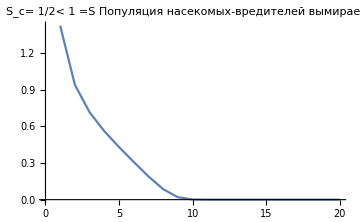

```mathematica
ClearAll[M,R,S];
M=1; R=3;S=1;
ListPlot[RecurrenceTable[{NN[n+1]==(R (NN[n])^2)/(((R-1)(NN[n])^2)/M+NN[n]+S),NN[0]==10},NN,{n,1,20}],Joined->True,PlotLabel->StringForm["S_c= ``< `` =S\n Популяция насекомых-вредителей вымирает :(",NumberForm[1/4 M (-1+R),4],NumberForm[S,4]],ImageSize->Medium]
```

Популяция насекомых-вредителей не вымирает при M=1, R=7, S=1, то есть S_c≥S

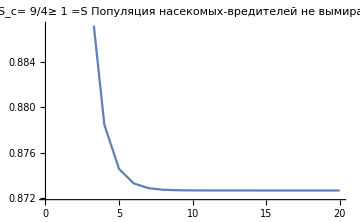

```mathematica
ClearAll[M,R,S];
M=1; R=10;S=1;
ListPlot[RecurrenceTable[{NN[n+1]==(R (NN[n])^2)/(((R-1)(NN[n])^2)/M+NN[n]+S),NN[0]==10},NN,{n,1,20}],Joined->True,PlotLabel->StringForm["S_c= ``≥ `` =S\n Популяция насекомых-вредителей не вымирает :)",NumberForm[1/4 M (-1+R),4],NumberForm[S,4]],ImageSize->Medium]
```

## Задание 3. Бифуркационная диаграмма дискретной логистической модели

Рассмотрим дискретную логистическую модель

N_(n+1)=k N_n (1-N_n),  0<k≤4.

Известно, что для значений параметра 0<k<1 неподвижная точка N^*=0 является асимптотически устойчивой (аттрактор).  Это означает, что при любом начальном значении N_0 из окрестности неподвижной точки N^*=0 решение дискретной логистической модели стремится к N^*=0.

Построим решение дискретной логистической модели (4) с помощью функции RecurrenceTable при k=0.9 и начального состояния N_0=0.5 и убедимся, что решение стремится к нулю.

```mathematica
k=0.9;
```

```mathematica
data=RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==0.5},NN,{n,100,150}];
```

Определим координаты соответствующих точек и построим график

```mathematica
data = {Range[100,150],data}//Transpose;
```

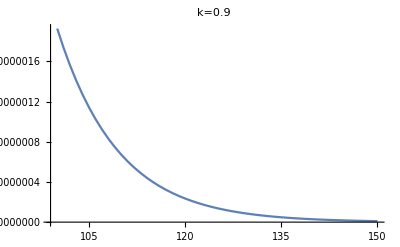

```mathematica
ListPlot[data,Joined->True,PlotLabel->"k=0.9"]
```

Известно, что для значений параметра 1<k<3 неподвижная точка N^*=1-1/k является асимптотически устойчивой (аттрактор).  Это означает, что при любом начальном значении N_0 из окрестности неподвижной точки N^*=1-1/k решение дискретной динамической системы стремится к значению N^*=1-1/k.

Построим решение дискретной динамической системы при k=2 и начального состояния N_0=0.5 и убедимся, что решение стремится к N^*=1-1/k=1/2.

```mathematica
k=2;
```

```mathematica
data=RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==0.5},NN,{n,100,150}];
```

```mathematica
data = {Range[100,150],data}//Transpose;
```

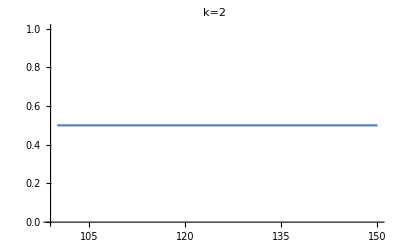

```mathematica
ListPlot[data,Joined->True,PlotLabel->"k=2"]
```

### Задание 3.1 (Анализ циклов длины 2)

Проанализируйте устойчивость неподвижных точек для композиции f^2(x) и покажите, что для значений 3<k≤1+√6≈3.449 периодические решения с циклом длины 2 являются асимптотически устойчивыми.

Построим решение дискретной динамической системы при k=3.4 и начального состояния N_0=0.1 и убедимся, что решение стремится к периодическому решению с циклом длины 2.

```mathematica
k=3.4;
```

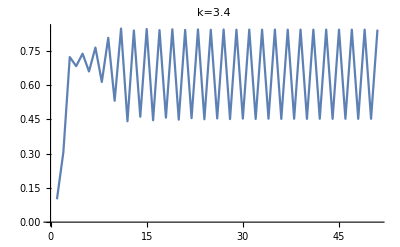

```mathematica
ListPlot[RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==0.1},NN,{n,0,50}],Joined->True,PlotLabel->"k=3.4"]
```

```mathematica
ClearAll[NN,a,k,n]
RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==a},NN,{n,0,2}]
```

{a,(1-a) a k,(1-a) a k^2 (1-(1-a) a k)}

```mathematica
sol=Solve[NN==(1-NN) NN k^2 (1-(1-NN) NN k),NN]//Values//Flatten//Simplify
```

{0,(-1+k)/k,(1+k-√(-3-2 k+k^2))/(2 k),(1+k+√(-3-2 k+k^2))/(2 k)}

```mathematica
D[(1-NN) NN k^2 (1-(1-NN) NN k),NN]//Simplify
```

-k^2 (-1+2 NN) (1+2 k (-1+NN) NN)

```mathematica
D[(1-NN) NN k^2 (1-(1-NN) NN k),NN]/.NN->sol⟦3⟧//Simplify
D[(1-NN) NN k^2 (1-(1-NN) NN k),NN]/.NN->sol⟦4⟧//Simplify
```

4+2 k-k^2

4+2 k-k^2

```mathematica
Reduce[Abs[4+2 k-k^2]<1,k,Reals]
```

1-√6<k<-1||3<k<1+√6

```mathematica
4+2 k-k^2/.k->{3+10^-5,1+√6-10^-5}//N
```

{0.99996,-0.999951}

### Задание 3.2 (Анализ циклов длины 4)

Проанализируйте устойчивость неподвижных точек для композиции f^4(x) и покажите, что для значений 3.449<k<3.54409 периодические решения с циклом длины 4 являются устойчивыми.

Построим решение дискретной динамической системы при k=3.5 и начального состояния N_0=0.1 и убедимся, что решение стремится к периодическому решению с циклом длины 4.

```mathematica
k=3.5;
```

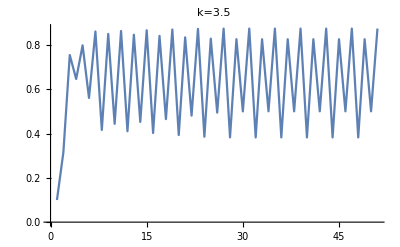

```mathematica
ListPlot[RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==0.1},NN,{n,0,50}],Joined->True,PlotLabel->"k=3.5"]
```

k^*≈3.569946 является пределом формирования циклов с периодом 2^m и при k^* осуществляется переход к хаотическому поведению решения дискретной логистической модели, т.е. при k>k^*≈3.569946 решение является непериодическим. Это пример детерминированного хаоса.

```mathematica
k=3.7;
```

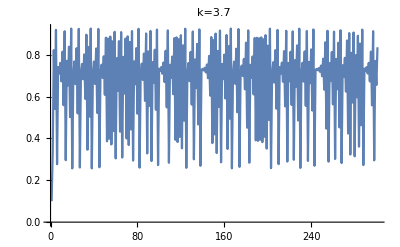

```mathematica
ListPlot[RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==0.1},NN,{n,0,300}],Joined->True,PlotLabel->"k=3.7"]
```

```mathematica
ClearAll[NN,a,k,n]
RecurrenceTable[{NN[n+1]==k NN[n](1-NN[n]),NN[0]==a},NN,{n,0,4}]
```

{a,(1-a) a k,(1-a) a k^2 (1-(1-a) a k),(1-a) a k^3 (1-(1-a) a k) (1-(1-a) a k^2 (1-(1-a) a k)),(1-a) a k^4 (1-(1-a) a k) (1-(1-a) a k^2 (1-(1-a) a k)) (1-(1-a) a k^3 (1-(1-a) a k) (1-(1-a) a k^2 (1-(1-a) a k)))}

```mathematica
sol1=(Solve[NN==(1-NN) NN k^4 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN)NN k))(1-(1-NN) NN k^3 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN) NN k))),NN]//Values//Flatten//Simplify)⟦5;; ⟧
```

{Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,1],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,2],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,3],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,4],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,5],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,6],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,7],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,8],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,9],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,10],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,11],Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,12]}

```mathematica
D[(1-NN) NN k^4 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN)NN k))(1-(1-NN) NN k^3 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN) NN k))),NN]//FullSimplify
```

-k^4 (-1+2 NN) (1+2 k (-1+NN) NN) (1+2 k^2 (-1+NN) NN (1+k (-1+NN) NN)) (1+2 k^3 (-1+NN) NN (1+k (-1+NN) NN) (1+k^2 (-1+NN) NN (1+k (-1+NN) NN)))

```mathematica
((D[(1-NN) NN k^4 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN)NN k))(1-(1-NN) NN k^3 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN) NN k))),NN]/.NN->sol1⟦#⟧)//Simplify)&/@Range[12]
%//Length
```

{-k^4 (-1+2 Root[1&,1]) (-3-4/k^2+(2 (4+2 k+5 k^2+k^3+k^4) Root[1+k^2+12+k^12 #1^12&,1])/k-(2 (4+4+k^6) 1^2)/k+9+20 k^7 (1+5 k) Root[1+k^2+12+k^12 #1^12&,1]^9-44 k^8 Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+8+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,1]^10+8 k^8 Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+5+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,1]^11),10,-k^4 (1) (18+1)}
 |  |  |  |

12

```mathematica
der1=(D[(1-NN) NN k^4 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN)NN k))(1-(1-NN) NN k^3 (1-(1-NN) NN k) (1-(1-NN) NN k^2 (1-(1-NN) NN k))),NN]/.NN->sol1⟦5⟧)
```

k^4 (1-Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,5]) 1 (1-1) (1-k^2 (1-Root[1+13+k^12 1&,5]) Root[1&,5] (1-k (1-Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+4+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,5]) Root[1+k^2+(-k^2-k^3-k^4-k^5) #1+(2 k^3+k^4+4 k^5+k^6+2 k^7) #1^2+(-k^3-5 k^5-4 k^6-5 k^7-4 k^8-k^9) #1^3+(2 k^5+6 k^6+4 k^7+14 k^8+5 k^9+3 k^10) #1^4+(-4 k^6-k^7-18 k^8-12 k^9-12 k^10-3 k^11) #1^5+(k^6+10 k^8+17 k^9+18 k^10+15 k^11+k^12) #1^6+(-2 k^8-14 k^9-12 k^10-30 k^11-6 k^12) #1^7+(6 k^9+3 k^10+30 k^11+15 k^12) #1^8+(-k^9-15 k^11-20 k^12) #1^9+(3 k^11+15 k^12) #1^10-6 k^12 #1^11+k^12 #1^12&,5])) (5+1)+5
 |  |  |  |

```mathematica
Reduce[Abs[der1]<1,k,Reals]
```

False

```mathematica
der1/.k->{3.449+10^-5,3.54409-10^-5}//N
```

Root::npoly: {12.8957-682.49 #1+15470.7 #1^2-187404. #1^3+1.37456×10^6 #1^4-6.52484×10^6 #1^5+2.08206×10^7 #1^6-4.55135×10^7 #1^7+6.82793×10^7 #1^8-6.90638×10^7 #1^9+«3»,13.5605-773.978 #1+18511. #1^2-233655. #1^3+1.76853×10^6 #1^4-8.59712×10^6 #1^5+2.79247×10^7 #1^6-6.18373×10^7 #1^7+9.36096×10^7 #1^8-9.52448×10^7 #1^9+«3»} is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

{1,1+5}
 |  |  |  |

Как можно заметить, определение устойчивости неподвижных точек для композиции f^4(x)  для значений 3.449<k<3.54409 периодические решения с циклом длины 4 является трудоспособным, так как вольфрам даже не может посчитать значение производной функции в неподвижной точке с заданным параметром k, не говоря уже об определение устойчивости на отрезке (интервале) через встроенную функцию Reduce.

### Задание 3.3 (Бифуркационная диаграмма)

Постройте бифуркационную диаграмму в фазово-параметрическом пространстве (k,N^*) для дискретной логистической модели (4) при 2≤k≤4.

-Graphics-

Обратите внимание на появление “светлых” промежутков с периодическим поведением при k>k^*≈3.569945.

#### Рекомендации по выполнению

Для построения решения дискретной логистической модели можно использовать следующую рекурсивную функцию

```mathematica
ClearAll[NN];
NN[k_][0]=0.5;
NN[k_][n_Integer?Positive]:=NN[k][n]=k NN[k][n-1]*(1-NN[k][n-1])
```

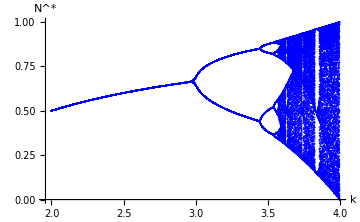

```mathematica
ListPlot[Transpose@Table[NN[k][n],{k,2,4,0.001},{n,100,150}],DataRange->{2,4},AxesLabel->{"k", "N^*"},ImageSize->Medium,PlotStyle->Blue]
```

Для построения бифуркационной диаграммы необходимо изменять значение параметра k с малым шагом, например, равным 0.001, и для каждого значения параметра изображать на графике значения соответствующего решения на итерациях 100≤n≤150, полагая, что заданные значения n  будут соответствовать установлению решения на неподвижных точках.

### Задание 3.4 (Свойство самоподобия решения)

Постройте бифуркационную диаграмму в фазово-параметрическом пространстве (k,N^*) для дискретной логистической модели (4) при 3.7≤k≤3.704.

-Graphics-

Это является иллюстрацией свойства самоподобия детерминированных систем с хаотическим поведением или фрактальной структуры решения, когда поведение фрагмента области подобно всей области.

```mathematica
ListPlot[Transpose@Table[NN[k][n],{k,3.7,3.704,10^-6},{n,100,150}],PlotRange->{0.7,0.708},DataRange->{3.7,3.704},AxesLabel->{"k", "N^*"},ImageSize->Medium,PlotStyle->Blue]
```

-Graphics-

## Задание 4. Бифуркационная диаграмма дискретной модели Рикера

Рассмотрим безразмерную модель Рикера (2) из Задания 1

N_(n+1)=N_n ⅇ^(k(1-N_n)), гдеk>0.

Постройте бифуркационную диаграмму в фазово-параметрическом пространстве (k,N^*) для модели Рикера при k>0.

```mathematica
ClearAll[NN1];
NN1[k_][0]=0.5;
NN1[k_][n_Integer?Positive]:=NN1[k][n]=NN1[k][n-1]*ⅇ^(k(1-NN1[k][n-1]))
```

```mathematica
ListPlot[Transpose@Table[NN1[k][n],{k,0.001,4,0.001},{n,100,150}],DataRange->{0.001,4},AxesLabel->{"k", "N^*"},ImageSize->Medium,PlotStyle->Blue]
```

-Graphics-

## Задание 5. Генерация последовательности псевдослучайных чисел

Существование режимов хаотического поведения дискретных динамических систем используется для построения последовательностей псевдослучайных чисел.

Примером может служить следующая дискретная динамическая система для генерации чисел, равномерно распределенных на отрезке [0,1]

x_(n+1)=|100Log[x_n]  mod 1|,

где остаток от деления на 1 возвращает дробную часть для положительного числа

```mathematica
{Mod[0.3,1],Mod[-0.3,1]}
```

{0.3,0.7}

Для генерации последовательности псевдослучайных чисел используется начальное состояние x_0=0.1

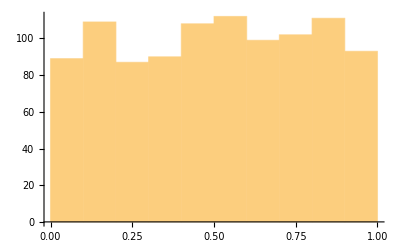

```mathematica
Histogram@RecurrenceTable[{x[n+1]==Abs[Mod[100Log[x[n]],1]],x[0]==0.1},x, {n,1,1000}]
```

### Задание 5.1 (Сравнение)

Сравните математическое ожидание (Mean) и дисперсию (Variance) для сгенерированной последовательности с аналогичными характеристиками встроенной функции UniformDistribution, имитирующей непрерывное равномерное распределение случайной величины на заданном отрезке.

```mathematica
Import["example1.png"]
```

-Graphics-

```mathematica
Import["example2.png"]
```

-Graphics-

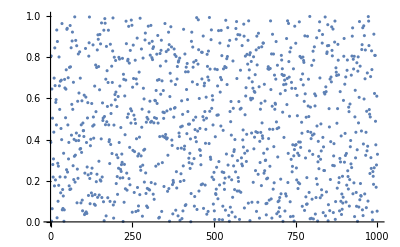

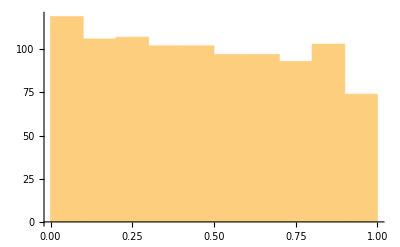

```mathematica
data=RandomVariate[UniformDistribution[{0,1}],1000];
ListPlot@ data
Histogram@ data
```

```mathematica
Median[UniformDistribution[{min,max}]]
Median[UniformDistribution[]]
```

(max+min)/2

1/2

```mathematica
Mean[UniformDistribution[{min,max}]]
Mean[UniformDistribution[]]
```

(max+min)/2

1/2

```mathematica
Variance[UniformDistribution[{min,max}]]
Variance[UniformDistribution[]]
```

1/12 (max-min)^2

1/12

```mathematica
StandardDeviation[UniformDistribution[{min,max}]]
StandardDeviation[UniformDistribution[]]
```

(max-min)/(2 √3)

1/(2 √3)

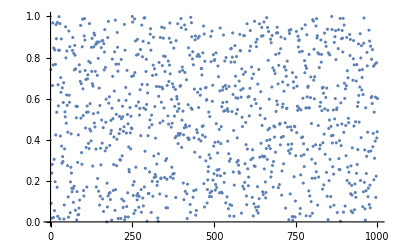

-Graphics-

```mathematica
data1=RecurrenceTable[{x[n+1]==Abs[Mod[100Log[x[n]],1]],x[0]==0.1},x, {n,1,1000}];
ListPlot[data1]
Histogram@data1
```

```mathematica
Mean[data]
Mean[data1]
```

0.473425

0.507078

```mathematica
Median[data]
Median[data1]
```

0.463366

0.518472

```mathematica
Variance[data]
Variance[data1]
```

0.0821757

0.0812488

```mathematica
StandardDeviation[data]
StandardDeviation[data1]
```

0.286663

0.285042

### Задание 5.2 (Дискретная динамическая система)

Найдите в литературе другой пример дискретной динамической системы для генерации псевдослучайных чисел, например, см. [6]. Укажите ссылку на источник, который Вы нашли. 

Изобразите случайные числа, вычислите математическое ожидание и дисперсию, сравните с аналогичными характеристиками встроенной функции, имитирующей соответствующее распределение (например, UniformDistribution, NormalDistribution, LogNormalDistribution, BetaDistribution, BinomialDistribution, NegativeBinomialDistribution, PoissonDistribution).

```mathematica
Names["*Distribution"]//Length
```

166

```mathematica
Mean[LogNormalDistribution[n,p]]
Median[LogNormalDistribution[n,p]]
Variance[LogNormalDistribution[n,p]]
StandardDeviation[LogNormalDistribution[n,p]]
```

ⅇ^(n+p^2/2)

ⅇ^n

ⅇ^(2 n+p^2) (-1+ⅇ^(p^2))

√(ⅇ^(2 n+p^2) (-1+ⅇ^(p^2)))

```mathematica
Mean[NormalDistribution[n,p]]
Median[NormalDistribution[n,p]]
Variance[NormalDistribution[n,p]]
StandardDeviation[NormalDistribution[n,p]]
```

n

n

p^2

p

```mathematica
Mean[BinomialDistribution[n,p]]
Median[BinomialDistribution[n,p]]
Variance[BinomialDistribution[n,p]]
StandardDeviation[BinomialDistribution[n,p]]
```

n p

Median[BinomialDistribution[n,p]]

n (1-p) p

√(n (1-p) p)

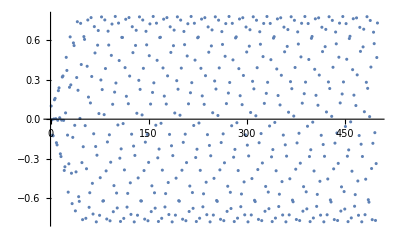

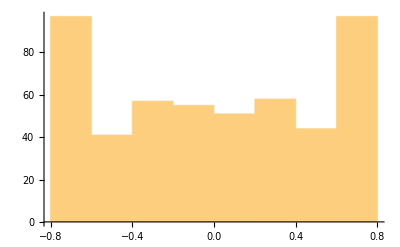

```mathematica
ClearAll[y];
Subscript[λ, 1]=0.105;
Subscript[λ, 2]=-0.158;
ψ=0.998;
gen=RecurrenceTable[{y[n]==Subscript[λ, 1]*y[n-1]+Subscript[λ, 2]*y[n-2]+ ψ*(1-(y[n-1])^2)*(y[n-1]-y[n-2]),y[0]==0.1,y[1]==0.1},y,{n,1,500}];
ListPlot@gen1
Histogram@gen1
```

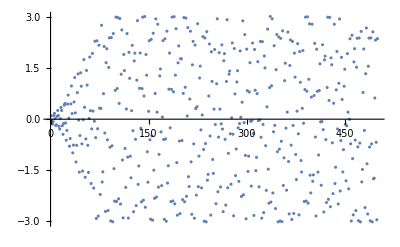

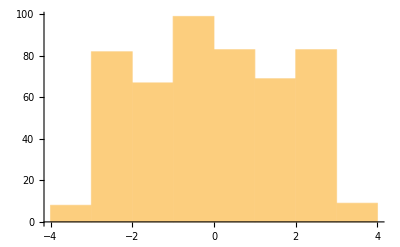

```mathematica
ClearAll[y];
Subscript[λ, 1]=0.605;
Subscript[λ, 2]=-0.958;
ψ=0.198;
gen1=RecurrenceTable[{y[n]==Subscript[λ, 1]*y[n-1]+Subscript[λ, 2]*y[n-2]+ ψ*(1-(y[n-1])^2)*(y[n-1]-y[n-2]),y[0]==0.1,y[1]==0.1},y,{n,1,500}];
ListPlot@gen1
Histogram@gen1
```

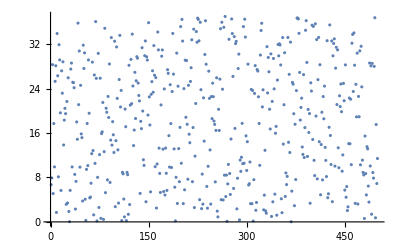

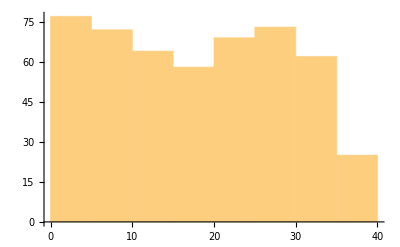

```mathematica
ClearAll[X,a,c,m];
a = 17;
c=5;
m =37;
gen2=RecurrenceTable[{X[n+1]==Mod[a X[n]+c,m], X[0]==0.1},X,{n,1,500}];
ListPlot@gen2
Histogram@gen2
```

```mathematica
ClearAll[X,a,c,m];
a = 5;
c=19;
m =17;
gen3=RecurrenceTable[{X[n+1]==Mod[a X[n]+c,m], X[0]==0.1},X,{n,1,500}];
ListPlot@gen2
Histogram@gen2
```

-Graphics-

-Graphics-

```mathematica
Mean[gen]
Mean[gen1]
Mean[gen2]
Mean[gen3]
```

0.00102741

-0.00321507

18.0959

7.984

```mathematica
Median[gen]
Median[gen1]
Median[gen2]
Median[gen3]
```

-0.00197147

-0.0440922

18.1273

7.5

```mathematica
StandardDeviation[gen]
StandardDeviation[gen1]
StandardDeviation[gen2]
StandardDeviation[gen3]
```

0.518967

1.79387

10.7951

4.62434

```mathematica
Variance[gen]
Variance[gen1]
Variance[gen2]
Variance[gen3]
```

0.269327

3.21797

116.534

21.3845

Ссылки на примеры дискретной динамической системы для генерации псевдослучайных чисел:
https://cyberleninka.ru/article/n/o-postroenii-programmnyh-generatorov-psevdosluchaynyh-chisel-na-osnove-dinamicheskih-sistem-v-rezhime-determinirovannogo-haosa/viewer - gen, gen1
https://ru.wikipedia.org/wiki/%D0%93%D0%B5%D0%BD%D0%B5%D1%80%D0%B0%D1%82%D0%BE%D1%80_%D0%BF%D1%81%D0%B5%D0%B2%D0%B4%D0%BE%D1%81%D0%BB%D1%83%D1%87%D0%B0%D0%B9%D0%BD%D1%8B%D1%85_%D1%87%D0%B8%D1%81%D0%B5%D0%BB - gen2, gen3
Как можно заметить, медианное, стандартное отклонение, математическое ожидание и дисперсию вычисляются по-разному, в зависимости от введенных начальных данных и разных дискретных динамических систем для генерации псевдослучайных чисел. Однако алгоритм их вычисления определяется одинаковым способом, как показано на картинках в задании 5.1.Сравнение с аналогичными характеристиками встроенной функции, имитирующей соответствующее распределение дали понять, что каждый метод используют разные методы для высчитывания распределения случайных величин и каждому заданию требуется тщательный подбор конкретной функции распределения для выбранной нами модели.

## Литература

[1] А. С. Братусь, А. С. Новожилов, А. П. Платонов. Динамические системы и модели биологии. -- 2011.

[2] М. Г. Юмагулов. Введение в теорию динамических систем. -- СПб.: Издательство “Лань”, 2015.

[3] S. Lynch. Dynamical Systems with Applications using Mathematica.. -- Birkhauser, 2007.

[4] J. D. Murray. Mathematical biology. I. An introduction. -- Springer, 2002.

[5] R. A. Holmgren. A first course in discrete dynamical systems. -- Springer, 1996.

[6] Д. Кнут. Искусство программирования для ЭВМ. Т.2: . -- М.: Мир, 1977.

[7] Д. Мюррей. Математическая биология. Т.1. Введение: . -- М.-Ижевск: НИЦ “Регулярная и хаотическая динамика”, Институт компьютерных исследований, 2009.